## Model

#### Resource

```mathematica
net =NetModel["GPT2 Transformer Trained on WebText Data"]
```

NetChain[<>]

```mathematica
lm=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"}]
```

NetChain[<>]

#### Information

```mathematica
Information[net,"ArraysElementCounts"]
```

<|NetArray[…]→38597376,{decoder,13,Biases}→768,{decoder,13,Scaling}→768,{embedding,embeddingpos,Weights}→786432,{decoder,1,1,norm,Biases}→768,{decoder,1,1,norm,Scaling}→768,{decoder,1,2,norm,Biases}→768,{decoder,1,2,norm,Scaling}→768,{decoder,10,1,norm,Biases}→768,{decoder,10,1,norm,Scaling}→768,{decoder,10,2,norm,Biases}→768,{decoder,10,2,norm,Scaling}→768,{decoder,11,1,norm,Biases}→768,{decoder,11,1,norm,Scaling}→768,{decoder,11,2,norm,Biases}→768,{decoder,11,2,norm,Scaling}→768,{decoder,12,1,norm,Biases}→768,{decoder,12,1,norm,Scaling}→768,{decoder,12,2,norm,Biases}→768,{decoder,12,2,norm,Scaling}→768,{decoder,2,1,norm,Biases}→768,{decoder,2,1,norm,Scaling}→768,{decoder,2,2,norm,Biases}→768,{decoder,2,2,norm,Scaling}→768,{decoder,3,1,norm,Biases}→768,{decoder,3,1,norm,Scaling}→768,{decoder,3,2,norm,Biases}→768,{decoder,3,2,norm,Scaling}→768,{decoder,4,1,norm,Biases}→768,{decoder,4,1,norm,Scaling}→768,{decoder,4,2,norm,Biases}→768,{decoder,4,2,norm,Scaling}→768,{decoder,5,1,norm,Biases}→768,{decoder,5,1,norm,Scaling}→768,{decoder,5,2,norm,Biases}→768,{decoder,5,2,norm,Scaling}→768,{decoder,6,1,norm,Biases}→768,{decoder,6,1,norm,Scaling}→768,{decoder,6,2,norm,Biases}→768,{decoder,6,2,norm,Scaling}→768,{decoder,7,1,norm,Biases}→768,{decoder,7,1,norm,Scaling}→768,{decoder,7,2,norm,Biases}→768,{decoder,7,2,norm,Scaling}→768,{decoder,8,1,norm,Biases}→768,{decoder,8,1,norm,Scaling}→768,{decoder,8,2,norm,Biases}→768,{decoder,8,2,norm,Scaling}→768,{decoder,9,1,norm,Biases}→768,{decoder,9,1,norm,Scaling}→768,{decoder,9,2,norm,Biases}→768,{decoder,9,2,norm,Scaling}→768,{decoder,1,2,linear1,Net,Biases}→3072,{decoder,1,2,linear1,Net,Weights}→2359296,{decoder,1,2,linear2,Net,Biases}→768,{decoder,1,2,linear2,Net,Weights}→2359296,{decoder,10,2,linear1,Net,Biases}→3072,{decoder,10,2,linear1,Net,Weights}→2359296,{decoder,10,2,linear2,Net,Biases}→768,{decoder,10,2,linear2,Net,Weights}→2359296,{decoder,11,2,linear1,Net,Biases}→3072,{decoder,11,2,linear1,Net,Weights}→2359296,{decoder,11,2,linear2,Net,Biases}→768,{decoder,11,2,linear2,Net,Weights}→2359296,{decoder,12,2,linear1,Net,Biases}→3072,{decoder,12,2,linear1,Net,Weights}→2359296,{decoder,12,2,linear2,Net,Biases}→768,{decoder,12,2,linear2,Net,Weights}→2359296,{decoder,2,2,linear1,Net,Biases}→3072,{decoder,2,2,linear1,Net,Weights}→2359296,{decoder,2,2,linear2,Net,Biases}→768,{decoder,2,2,linear2,Net,Weights}→2359296,{decoder,3,2,linear1,Net,Biases}→3072,{decoder,3,2,linear1,Net,Weights}→2359296,{decoder,3,2,linear2,Net,Biases}→768,{decoder,3,2,linear2,Net,Weights}→2359296,{decoder,4,2,linear1,Net,Biases}→3072,{decoder,4,2,linear1,Net,Weights}→2359296,{decoder,4,2,linear2,Net,Biases}→768,{decoder,4,2,linear2,Net,Weights}→2359296,{decoder,5,2,linear1,Net,Biases}→3072,{decoder,5,2,linear1,Net,Weights}→2359296,{decoder,5,2,linear2,Net,Biases}→768,{decoder,5,2,linear2,Net,Weights}→2359296,{decoder,6,2,linear1,Net,Biases}→3072,{decoder,6,2,linear1,Net,Weights}→2359296,{decoder,6,2,linear2,Net,Biases}→768,{decoder,6,2,linear2,Net,Weights}→2359296,{decoder,7,2,linear1,Net,Biases}→3072,{decoder,7,2,linear1,Net,Weights}→2359296,{decoder,7,2,linear2,Net,Biases}→768,{decoder,7,2,linear2,Net,Weights}→2359296,{decoder,8,2,linear1,Net,Biases}→3072,{decoder,8,2,linear1,Net,Weights}→2359296,{decoder,8,2,linear2,Net,Biases}→768,{decoder,8,2,linear2,Net,Weights}→2359296,{decoder,9,2,linear1,Net,Biases}→3072,{decoder,9,2,linear1,Net,Weights}→2359296,{decoder,9,2,linear2,Net,Biases}→768,{decoder,9,2,linear2,Net,Weights}→2359296,{decoder,1,1,attention,1,Net,Biases}→768,{decoder,1,1,attention,1,Net,Weights}→589824,{decoder,1,1,attention,2,Net,Biases}→768,{decoder,1,1,attention,2,Net,Weights}→589824,{decoder,1,1,attention,4,Net,Biases}→768,{decoder,1,1,attention,4,Net,Weights}→589824,{decoder,1,1,attention,6,Net,Biases}→768,{decoder,1,1,attention,6,Net,Weights}→589824,{decoder,10,1,attention,1,Net,Biases}→768,{decoder,10,1,attention,1,Net,Weights}→589824,{decoder,10,1,attention,2,Net,Biases}→768,{decoder,10,1,attention,2,Net,Weights}→589824,{decoder,10,1,attention,4,Net,Biases}→768,{decoder,10,1,attention,4,Net,Weights}→589824,{decoder,10,1,attention,6,Net,Biases}→768,{decoder,10,1,attention,6,Net,Weights}→589824,{decoder,11,1,attention,1,Net,Biases}→768,{decoder,11,1,attention,1,Net,Weights}→589824,{decoder,11,1,attention,2,Net,Biases}→768,{decoder,11,1,attention,2,Net,Weights}→589824,{decoder,11,1,attention,4,Net,Biases}→768,{decoder,11,1,attention,4,Net,Weights}→589824,{decoder,11,1,attention,6,Net,Biases}→768,{decoder,11,1,attention,6,Net,Weights}→589824,{decoder,12,1,attention,1,Net,Biases}→768,{decoder,12,1,attention,1,Net,Weights}→589824,{decoder,12,1,attention,2,Net,Biases}→768,{decoder,12,1,attention,2,Net,Weights}→589824,{decoder,12,1,attention,4,Net,Biases}→768,{decoder,12,1,attention,4,Net,Weights}→589824,{decoder,12,1,attention,6,Net,Biases}→768,{decoder,12,1,attention,6,Net,Weights}→589824,{decoder,2,1,attention,1,Net,Biases}→768,{decoder,2,1,attention,1,Net,Weights}→589824,{decoder,2,1,attention,2,Net,Biases}→768,{decoder,2,1,attention,2,Net,Weights}→589824,{decoder,2,1,attention,4,Net,Biases}→768,{decoder,2,1,attention,4,Net,Weights}→589824,{decoder,2,1,attention,6,Net,Biases}→768,{decoder,2,1,attention,6,Net,Weights}→589824,{decoder,3,1,attention,1,Net,Biases}→768,{decoder,3,1,attention,1,Net,Weights}→589824,{decoder,3,1,attention,2,Net,Biases}→768,{decoder,3,1,attention,2,Net,Weights}→589824,{decoder,3,1,attention,4,Net,Biases}→768,{decoder,3,1,attention,4,Net,Weights}→589824,{decoder,3,1,attention,6,Net,Biases}→768,{decoder,3,1,attention,6,Net,Weights}→589824,{decoder,4,1,attention,1,Net,Biases}→768,{decoder,4,1,attention,1,Net,Weights}→589824,{decoder,4,1,attention,2,Net,Biases}→768,{decoder,4,1,attention,2,Net,Weights}→589824,{decoder,4,1,attention,4,Net,Biases}→768,{decoder,4,1,attention,4,Net,Weights}→589824,{decoder,4,1,attention,6,Net,Biases}→768,{decoder,4,1,attention,6,Net,Weights}→589824,{decoder,5,1,attention,1,Net,Biases}→768,{decoder,5,1,attention,1,Net,Weights}→589824,{decoder,5,1,attention,2,Net,Biases}→768,{decoder,5,1,attention,2,Net,Weights}→589824,{decoder,5,1,attention,4,Net,Biases}→768,{decoder,5,1,attention,4,Net,Weights}→589824,{decoder,5,1,attention,6,Net,Biases}→768,{decoder,5,1,attention,6,Net,Weights}→589824,{decoder,6,1,attention,1,Net,Biases}→768,{decoder,6,1,attention,1,Net,Weights}→589824,{decoder,6,1,attention,2,Net,Biases}→768,{decoder,6,1,attention,2,Net,Weights}→589824,{decoder,6,1,attention,4,Net,Biases}→768,{decoder,6,1,attention,4,Net,Weights}→589824,{decoder,6,1,attention,6,Net,Biases}→768,{decoder,6,1,attention,6,Net,Weights}→589824,{decoder,7,1,attention,1,Net,Biases}→768,{decoder,7,1,attention,1,Net,Weights}→589824,{decoder,7,1,attention,2,Net,Biases}→768,{decoder,7,1,attention,2,Net,Weights}→589824,{decoder,7,1,attention,4,Net,Biases}→768,{decoder,7,1,attention,4,Net,Weights}→589824,{decoder,7,1,attention,6,Net,Biases}→768,{decoder,7,1,attention,6,Net,Weights}→589824,{decoder,8,1,attention,1,Net,Biases}→768,{decoder,8,1,attention,1,Net,Weights}→589824,{decoder,8,1,attention,2,Net,Biases}→768,{decoder,8,1,attention,2,Net,Weights}→589824,{decoder,8,1,attention,4,Net,Biases}→768,{decoder,8,1,attention,4,Net,Weights}→589824,{decoder,8,1,attention,6,Net,Biases}→768,{decoder,8,1,attention,6,Net,Weights}→589824,{decoder,9,1,attention,1,Net,Biases}→768,{decoder,9,1,attention,1,Net,Weights}→589824,{decoder,9,1,attention,2,Net,Biases}→768,{decoder,9,1,attention,2,Net,Weights}→589824,{decoder,9,1,attention,4,Net,Biases}→768,{decoder,9,1,attention,4,Net,Weights}→589824,{decoder,9,1,attention,6,Net,Biases}→768,{decoder,9,1,attention,6,Net,Weights}→589824|>

#### Structure

```mathematica
NetExtract[net, "embedding"]
```

NetGraph[<>]

```mathematica
NetExtract[net, {"decoder",1,1}]
```

NetGraph[<>]

```mathematica
NetExtract[net, {"decoder",1,2}]
```

NetGraph[<>]

## Usage

#### Feature Extraction

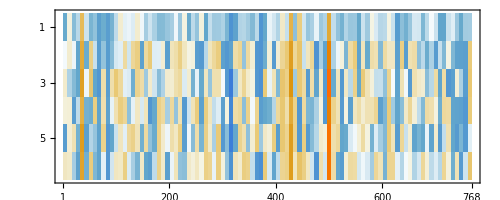

```mathematica
embeddings=net["The cat is on the mat"];
MatrixPlot[embeddings]
```

```mathematica
Dimensions[net["Hello I am cat"]]
```

{4,768}

```mathematica
Dimensions[net["The cat is on the mat"]]
```

{6,768}

#### Generate text

```mathematica
generateSample[languagemodel_][input_String,numTokens_:10,temperature_:1]:=Nest[Function[StringJoin[#,languagemodel[#,{"RandomSample","Temperature"->temperature}]]],input,numTokens];
```

```mathematica
generateSample[lm]["Albert Einstein was a German-born theoretical physicist",100,0.5]
```

Albert Einstein was a German-born theoretical physicist. He wrote a paper in 1846 Cycles of Light that predicted that the Sun's motion would be accelerated by the gravitational pull of the Sun, and that such an acceleration would be dependent on the mass of the Sun. Einstein's paper was published in 1846, and in 1847nergies were discovered, and the Sun was in a state of gravitational flux.


The theory that the Sun is in a state of gravitationalIENCE is called the general theory of relativity, and it is

```mathematica
generateSample[lm]["Nero loves Amo", 50,0.5]
```

Nero loves Amo smoking. He's a big fan of the cigar and he loves making good cigars. He's not a Typesetter, but he's got good technique. He's had a couple of great years with this cigar, and he's a good cigar smoker

```mathematica
generateSample[lm]["Amo loves Nero", 50,0.5]
```

Amo loves Nero's "Top of tympani" and the "Youngest of the gang" from the film. He also does a lot of the talking on the set, including a lot of the lines. HeAbsentee is also a fan of the

```mathematica
generateSample[lm]["Nero is a theoretical computer scientist", 50,0.05]
```

Nero is a theoretical computer scientist at the University of California, Berkeley. He is the author of "The Orion Nebula: A New Theory of the Universe," which was published in the journal Nature in Deaths blaze.


"The Orion Nebula is a very interesting and exciting discovery

```mathematica
generateSample[lm]["Nero does not have memories", 50,0.5]
```

Nero does not have memories of the time he spent with his brother. He is also a very good friend of Ryo and is very much a part of the team.

 Reporter: He has heard about the memory loss and hopes to see it in the future.

```mathematica
generateSample[lm]["GPT2 is a garbage.", 50,0.5]
```

GPT2 is a garbage.


In the past, the simple "no" was a good thing. In the future, you'll need NextGEN to do the same.


The only real keynote that I really want to talkJA is the new "TOD

```mathematica
generateSample[lm]["GPT2 is shit", 50,0.5]
```

GPT2 is shit.


There's no way I could have done it without a lot of help from my friends.


I'm pretty much the only one who can do421.


I'm also pretty much the only one who can do421